```mathematica
Clear[aliq]
aliq[0]=0;
aliq[x_]:=aliq[x]=If[x==0,0,DivisorSigma[1,x]-x];
```

```mathematica
Clear[l]
l[k_,n_]:=l[k,n]=NestList[aliq,k,n];
```

```mathematica
l[552,400],
```

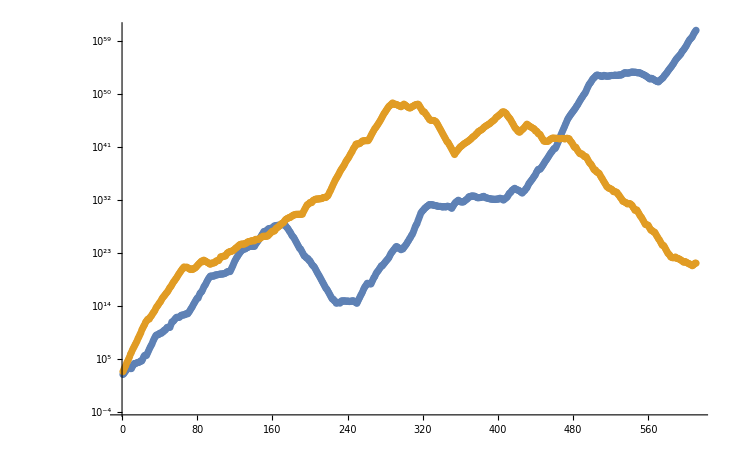
{80.044,-Graphics-}

```mathematica
ListLogPlot[{l[276,610],l[840,610]}]//Timing
```

```mathematica
l[840,800];//Timing
```

{47.972,Null}

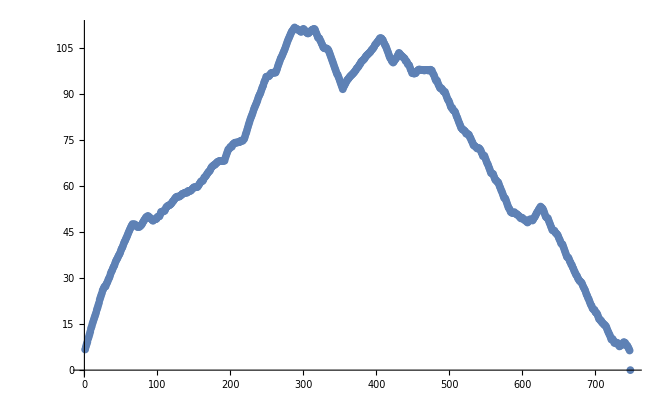

```mathematica
ListPlot[Log/@l[840,750]]
```